## Section | Roots versus Radicals

Sometimes there is great utility in having a closed-form expression—and all readers  will be familiar with the general solution to the quadratic equation.

Solve the general quadratic equation:

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

The key idea lying behind these expressions is the computation of the Discriminant, which, in general, is the product over all pairs of roots x_i, x_j of (x_i-x_j)^2.

Compute  the Discriminant of the general quadratic equation:

```mathematica
Discriminant[a x^2+b x+c,x]
```

b^2-4 a c

However, Physicists and engineers have a somewhat unhealthy obsession with “closed-form”

```mathematica
(x+b/2)^2==(b^2-4c)/4//FullSimplify//ExpandAll
```

c+b x+x^2==0

```mathematica
(2x+b)^2==b^2-4c//FullSimplify//ExpandAll
```

c+b x+x^2==0

## Roots of Polynomials

### Newton’s Method

Newton’s method or Newton-Raphson iteration is the “standard” method for finding the roots of a function:

In numerical analysis, Newton’s method, also known as the Newton–Raphson method, named after Isaac Newton and Joseph Raphson, is a root-finding algorithm which produces successively better approximations to the roots (or zeroes) of a real-valued function

While there are many ways to structure the code for an iterative method, probably the cleanest way is to combine a for loop with a break statement. As a very simple example, let F(x)=x/2. This method converges to x=0 independent of starting point.

Problem 1. Write a function that accepts a function f, an initial guess x_0, the derivative f', a stopping tolerance defaulting to 10^-5 and a maximum number of iterations defaulting to 15. Use Newton’s method as described in (9.3) to compute a zero x̄ of f. Terminate the algorithm when Abs[x_k-x_(k-1)] is less than the stopping tolerance or after iterating the maximum number of allowed times. Return the last computed approximation to x̄, a boolean value indicating whether or not the algorithm converged, and the number of iterations completed.

Test your function against functions like f(x)= ⅇ^x-2 (see Figure 9.1) or f(x)=x^4-3. Check that the computed zero x̄ satisfies f(x̄)≈0.

Also consider comparing your function to scipy.optimize.newton(), which accepts similar arguments.

```mathematica
NewtonsMethod[f_,x0_,ε_:10^-5,n_:15]:=
FixedPointList[x↦x-f[x]/f'[x],x0,n,SameTest->({u,v}↦Abs[u-v]<ε)]
```

```mathematica
f[x_]:=ⅇ^x-2
```

```mathematica
NewtonsMethod[f,1.]
```

{1.,0.735759,0.694042,0.693148,0.693147}

```mathematica
f[x_]:=x^4-3
```

```mathematica
NewtonsMethod[f,1`20,10^-15]
```

{1.,1.5,1.347222222222222222,1.31713769380343964,1.31607530075400562,1.31607401295438266,1.3160740129524925,1.3160740129524925}

```mathematica
f@Last@%
```

0.

```mathematica
Chop[%,10^-15]
```

0

```mathematica
FindRoot[f[x],{x,1},PrecisionGoal->15,WorkingPrecision->20]
```

{x→1.3160740129524924608}

```mathematica
FindRoot[f[x],{x,1},AccuracyGoal->18,WorkingPrecision->20]
```

{x→1.3160740129524924608}

```mathematica
f[x]/.%
```

0.

```mathematica
Options@FindRoot
```

{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

### As Radicals

The roots of cubic and quartic polynomials can, of course, be represented using radicals.

Compute the roots of x^3+α x+1:x

```mathematica
cubicroots=Solve[x^3+α x+1==0,x]
```

{{x→-((2/3)^(1/3) α)/((-9+√3 √(27+4 α^3))^(1/3))+((-9+√3 √(27+4 α^3))^(1/3))/(2^(1/3) 3^(2/3))},{x→((1+ⅈ √3) α)/(2^(2/3) 3^(1/3) (-9+√3 √(27+4 α^3))^(1/3))-((1-ⅈ √3) (-9+√3 √(27+4 α^3))^(1/3))/(2 2^(1/3) 3^(2/3))},{x→((1-ⅈ √3) α)/(2^(2/3) 3^(1/3) (-9+√3 √(27+4 α^3))^(1/3))-((1+ⅈ √3) (-9+√3 √(27+4 α^3))^(1/3))/(2 2^(1/3) 3^(2/3))}}

The roots of this irreducible cubic are all real for α=-2. However, this is not obvious from the explicit solution:

```mathematica
cubicroots/.α->-2
```

{{x→(1/2 (-9+ⅈ √15))^(1/3)/3^(2/3)+2/(3/2 (-9+ⅈ √15))^(1/3)},{x→-((1-ⅈ √3) (1/2 (-9+ⅈ √15))^(1/3))/(2 3^(2/3))-(1+ⅈ √3)/(3/2 (-9+ⅈ √15))^(1/3)},{x→-((1+ⅈ √3) (1/2 (-9+ⅈ √15))^(1/3))/(2 3^(2/3))-(1-ⅈ √3)/(3/2 (-9+ⅈ √15))^(1/3)}}

Small numeric error from round-off gives small imaginary parts:

```mathematica
N[%,20]
```

{{x→1.+0. ⅈ},{x→-1.6180339887498948482+0. ⅈ},{x→0.6180339887498948482+0. ⅈ}}

The small imaginary parts can be eliminated using Chop:

```mathematica
Chop@%
```

{{x→1.},{x→-1.6180339887498948482},{x→0.6180339887498948482}}

As expected, the irreducible cubic factors for α=-2:

```mathematica
Factor[x^3-2 x+1]
```

(-1+x) (-1+x+x^2)

Including an appropriate Extension full factorization is possible:

```mathematica
Factor[x^3-2 x+1,Extension->√5]
```

-1/4 (-1+√5-2 x) (-1+x) (1+√5+2 x)

Alternatively, in this case, one can obtain the roots directly:

```mathematica
cubicroots/.α->-2//FullSimplify
```

{{x→1},{x→1/2 (-1-√5)},{x→2/(1+√5)}}

### As Root Objects

While an explicit form may be useful in some cases, it is nearly always better to express the roots as Root objects—a concise way of expressing algebraic numbers via the minimal polynomial they satisfy, along with a canonical ordering in the complex plane (specified by the second argument of Root).

Using Reduce the roots of cubic and quartic polynomials are automatically represented as Root objects:

```mathematica
exactcubicroots=Reduce[x^3+α x+1==0,x]
```

x==Root[1+α #1+#1^3&,1]||x==Root[1+α #1+#1^3&,2]||x==Root[1+α #1+#1^3&,3]

```mathematica
exactcubicroots/.α->-2.
```

x==-1.61803||x==0.618034||x==1.

If all the polynomial coefficients are numerical, then an explicit approximation is returned, which can be evaluated to arbitrary precision:

```mathematica
Reduce[x^3+√3 x+1==0,x]
```

x==Root-0.504Root[{-3+#1^2&,1+#1 #2+#2^3&},{2,1}]-0.5036079131290119||x==Root0.252-1.39 ⅈRoot[{-3+#1^2&,1+#1 #2+#2^3&},{2,2}]0.25180395656450594||x==Root0.252+1.39 ⅈRoot[{-3+#1^2&,1+#1 #2+#2^3&},{2,3}]0.25180395656450594

To get a radical form, you can use ToRadicals:

```mathematica
ToRadicals[%]
```

x==-(2/(-3+√(9+4 √3)))^(1/3)/3^(1/6)+(1/6 (-3+√(9+4 √3)))^(1/3)||x==-1/2 (1+ⅈ √3) (1/6 (-3+√(9+4 √3)))^(1/3)+(1-ⅈ √3)/(2^(2/3) 3^(1/6) (-3+√(9+4 √3))^(1/3))||x==-1/2 (1-ⅈ √3) (1/6 (-3+√(9+4 √3)))^(1/3)+(1+ⅈ √3)/(2^(2/3) 3^(1/6) (-3+√(9+4 √3))^(1/3))

Clearly, this output is more complicated than the Root form.

## Which Form is Better?

In addition to size, there are many reasons to prefer the Root form over a radical expression:

It is typically faster to obtain.

It is numerically more stable to evaluate. In general, radical formulations are prone to numeric problems. Root objects do not have this liability.

When the roots of an irreducible cubic are all real, but not rational, the so-called “casus irreducibilis” shows that they still must be expressed in terms of ⅈ (see mathworld.wolfram.com/CasusIrreducibilis.html). This means that numeric evaluation will give small imaginary parts unless, by happenstance, they exactly cancel. Small numeric error from round off makes this unlikely.

For sufficiently complicated algebraics, it is often faster to evaluate the Root form numerically, at least at high precision.

Symmetric polynomial combinations of Root objects simplify using  RootReduce.

For applications in mathematics (e.g. Vieta jumping in number theory), engineering or physics one usually works with combinations of roots (e.g. applications of Routh-Hurwitz integrals) so Vieta's formulas relating the coefficients of a polynomial to sums and products of its roots is much more useful than explicit values for the roots.

Derivatives of Root objects with respect to a parameter are expressed in terms of Root objects. This is useful for eigenvalue sensitivity analysis.

For higher-order irreducible polynomials, radical representations do not exist in general. However, there are generalized hypergeometric representations (see Trott and Adamchik’s quintic poster and the example below).

One can sometimes avoid the Root form by using ToRadicals—but for all practical computation, you are better off working with Root objects.

### Examples

#### Derivatives

Compute the derivative of (the first root of) x^7-x+α with respect to the parameter α:

```mathematica
D[Root[x↦x^7-x+α,1], α]
```

-1/(-1+7 Root[α-#1+#1^7&,1]^6)

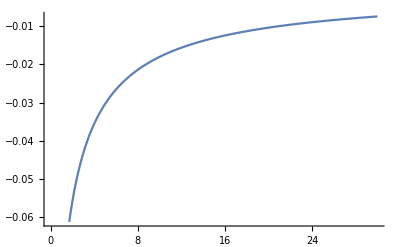

```mathematica
Plot[%,{α,0,30}]
```

#### Series Expansion

It is also easy to compute series expansions of Root objects. Here we expand the three roots of x^3-x+α==0 into a series in α:

```mathematica
Root[x↦x^3-x+α,1]+O[α]^7
```

-1-α/2+(3 α^2)/8-α^3/2+(105 α^4)/128-(3 α^5)/2+(3003 α^6)/1024+O[α]^7

```mathematica
Root[x↦x^3-x+α,2]+O[α]^7
```

α+α^3+3 α^5+O[α]^7

```mathematica
Root[x↦x^3-x+α,3]+O[α]^7
```

1-α/2-(3 α^2)/8-α^3/2-(105 α^4)/128-(3 α^5)/2-(3003 α^6)/1024+O[α]^7

The sum of these three roots vanishes up to this order as is expected since the coefficient of x^2 is zero:

```mathematica
%+%%+%%%
```

O[α]^7

#### Hypergeometric Representations

Solve the quintic x^5-x-α==0:

```mathematica
Solve[x^5-x-α==0,x]
```

{{x→Root[-α-#1+#1^5&,1]},{x→Root[-α-#1+#1^5&,2]},{x→Root[-α-#1+#1^5&,3]},{x→Root[-α-#1+#1^5&,4]},{x→Root[-α-#1+#1^5&,5]}}

For higher-order irreducible polynomials, radical representations do not exist in general:

```mathematica
ToRadicals[%]
```

{{x→Root[-α-#1+#1^5&,1]},{x→Root[-α-#1+#1^5&,2]},{x→Root[-α-#1+#1^5&,3]},{x→Root[-α-#1+#1^5&,4]},{x→Root[-α-#1+#1^5&,5]}}

However, there are generalized hypergeometric representations (see Trott and Adamchik’s quintic poster).

Compute the series expansion (of the second root) directly:

```mathematica
Root[x↦x^5-x-α,2]+O[α]^45
```

-α-α^5-5 α^9-35 α^13-285 α^17-2530 α^21-23751 α^25-231880 α^29-2330445 α^33-23950355 α^37-250543370 α^41+O[α]^45

Determine the coefficients:

```mathematica
CoefficientList[%,α]
```

{0,-1,0,0,0,-1,0,0,0,-5,0,0,0,-35,0,0,0,-285,0,0,0,-2530,0,0,0,-23751,0,0,0,-231880,0,0,0,-2330445,0,0,0,-23950355,0,0,0,-250543370}

Find a sequence that generates these coefficients using FindSequenceFunction:

```mathematica
FindSequenceFunction[%,n]
```

-((5^(-5/2+(5 n)/4) (1+(-1)^n-2 Cos[(n π)/2]) Gamma[-3/10+n/4] Gamma[-1/10+n/4] Gamma[1/10+n/4] Gamma[3/10+n/4])/(4 Gamma[1/5] Gamma[2/5] Gamma[3/5] Gamma[4/5] Gamma[n]))

Re-sum the series to find an explicit (generalized hypergeometric) representation of one of the roots, noting that the first term in the sequence corresponds to n==1:

```mathematica
r[α_]=∑_(n=1)^∞ % α^(n-1)
```

-α HypergeometricPFQ[{1/5,2/5,3/5,4/5},{1/2,3/4,5/4},(3125 α^4)/256]

Check this result by series expansion:

```mathematica
r[α]+O[α]^45
```

-α-α^5-5 α^9-35 α^13-285 α^17-2530 α^21-23751 α^25-231880 α^29-2330445 α^33-23950355 α^37-250543370 α^41+O[α]^45

Compute the second root of x^5-x+1/2 numerically:

```mathematica
N[Root[x↦x^5-x+1/2,2],45]
```

0.550606579334134968304020582185202073666608482

Compare with the hypergeometric representation:

```mathematica
%==r[-1/2]
```

True

More generally, the following family of hypergeometric functions have very simple minimal polynomials:

```mathematica
Table[{n,hyper=HypergeometricPFQ[Range[n-1]/n,Join[{n},Range[2,n-2]]/(n-1),n^n/(1-n)^(n-1)],MinimalPolynomial[RootApproximant@hyper][x]},{n,3,9}]
```

(3 | (2 sin(1/3 sin^-1((3 √3)/2)))/(√3) | x^3-x+1
4 | _3 F_2(1/4,1/2,3/4;2/3,4/3;-256/27) | x^4+x-1
5 | _4 F_3(1/5,2/5,3/5,4/5;1/2,3/4,5/4;3125/256) | x^5-x+1
6 | _5 F_4(1/6,1/3,1/2,2/3,5/6;2/5,3/5,4/5,6/5;-46656/3125) | x^6+x-1
7 | _6 F_5(1/7,2/7,3/7,4/7,5/7,6/7;1/3,1/2,2/3,5/6,7/6;823543/46656) | x^7-x+1
8 | _7 F_6(1/8,1/4,3/8,1/2,5/8,3/4,7/8;2/7,3/7,4/7,5/7,6/7,8/7;-16777216/823543) | x^8+x-1
9 | _8 F_7(1/9,2/9,1/3,4/9,5/9,2/3,7/9,8/9;1/4,3/8,1/2,5/8,3/4,7/8,9/8;387420489/16777216) | x^9-x+1)

### Newton's Method

Consider using Newton's method to compute the (complex) argument of the n-th roots of unity, i.e., the roots of f(z)=z^n-1. The Newton iteration, z→z-(f(z))/(f'(z)), becomes

```mathematica
z-(f(z))/(f'(z))/.f->(z↦z^n-1)//Simplify
```

(z (-1+n+z^-n))/n

To evaluate both f(z) and f'(z) we use a pure function replacement rule for f, f→Function(z,z^n-1).

The compiled function

```mathematica
NewtonIteration=Compile[{{n,_Integer},{c,_Complex}},Arg[FixedPoint[z↦(z (z^-n+n-1))/n,c,35]]];
```

can be used to show the convergence of points in the complex plane for specific n.

```mathematica
DensityPlot[NewtonIteration[3,x+ⅈ y],{x,1.1,-1.1},{y,-1.1,1.1},PlotPoints->200,Compiled->False,ColorFunction->Hue,ImageSize->Large]
```

-Graphics-

```mathematica
Clear@f
```

```mathematica
z-(f(z))/(f'(z))/.f->(z↦z^n-z)//Simplify
```

((-1+n) z^(1+n))/(-z+n z^n)

```mathematica
Solve[z^3-z==0,z]
```

{{z→-1},{z→0},{z→1}}

```mathematica
NewtonIteration=Compile[{{n,_Integer},{c,_Complex}},Arg[FixedPoint[z↦((-1+n) z^(1+n))/(-z+n z^n),c,35]]];
```

```mathematica
NewtonIteration[3,-2]
```

3.14159

```mathematica
NewtonIteration[3,2]
```

0.

```mathematica
NewtonIteration[3,1.2]
```

0.

```mathematica
DensityPlot[NewtonIteration[3,x+ⅈ y],{x,1.5,-1.5},{y,-1.5,1.5},PlotPoints->40,Compiled->False,ColorFunction->Hue,ImageSize->Large]
```

-Graphics-

Exercise. For n=4, visualize to which “attracting” root (out of ±1 and ±ⅈ) the Newton iteration converges. Note that the color of each point is determined by the Arg of the attracting root Arg({+1,-1,+ⅈ,-ⅈ}). Interpret the result. [4]

For fun, run the following code to produce an array of graphics (generated using GraphicsArray) that show the convergence of points in the complex plane, for n ranging from 5 to 13.

```mathematica
GraphicsGrid[Partition[Table[DensityPlot[NewtonIteration[n,x+ⅈ y],{x,1.1,-1.1},{y,-1.1,1.1},PlotPoints->50,Compiled->False,Frame->False],{n,5,13}],3],Spacings->Scaled[0.05]]
```

-Graphics-

## Transcendental Roots

In general, the implicit exact roots of transcendental equations can also expressed as Root objects.

Plot 0x+0x for 0<=x<=20:

```mathematica
Plot[BesselJ[0,x]+BesselY[0,x]==0,{x,0,20},Filling->Axis]
```

-Graphics-

Solve for the exact roots of 0x+0x==0 for 0<=x<=20:

```mathematica
Solve[{BesselJ[0,x]+BesselY[0,x]==0,0<=x<=20},x]
```

Solve::incs: Warning: Solve was unable to prove that the solution set found is complete.

{{x→},{x→},{x→},{x→},{x→},{x→},{x→}}

Compute the first root evaluated to 1000 decimal places:

```mathematica
N[x->Root"0.230"Root[{BesselJ[0,#1]+BesselY[0,#1]&,0.2303307811536659900625427186545106765477921636854761443858`30.102999566398122}]0.23033078115366598,1000]
```

x→0.2303307811536659900625427186545106765477921636854761443858514018001350571052712255153812482381283097804594745979526705225431556620592712680205318589484659197242508611724444480744702840099145134445909934516941570096254065188622483815298406418627410785856883429194231046708854134412817072496765240738319908337483336274116597382845433995305286811601498893702392998703948688961249816796678194506010253299563742187633011585019459066681127487055783567471338430737451705854315756932777985018388038955617968104406383453148746082927765925100939777476372389311442163715753905044293547008542854309110023351984488160860735329479668861098058341389868476132880696409291266726615758642017461416655947595137658759054897276279978074562542365398466922160603277798111770922380098085383403054871593457735801067270294528023916005296630956909104592768227047655332114807992662517119016877419496158622172404075871953904173942564708446882731286298361402593194338089755816929513974968622074880068378194566048355830479979300997

Verify this root:

```mathematica
BesselJ[0,x]+BesselY[0,x]/.%
```

0.

## Companion Matrix

The roots of a polynomial can be obtained from the eigenvalues of its companion matrix:

```mathematica
CompanionMatrix[poly_,x_]/;PolynomialQ[poly,x]:=Module[{n=Exponent[poly,x],coef},coef=CoefficientList[poly,x];coef=-Most[coef]/Last[coef];SparseArray[{{1,j_}:>coef⟦-j⟧,Band[{2,1}]->1},{n,n}]]
```

```mathematica
CompanionMatrix[x^5+∑_(k=0)^4 Subscript[a, k] x^k,x]//Normal
```

{{-a_4,-a_3,-a_2,-a_1,-a_0},{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0}}

```mathematica
-CharacteristicPolynomial[%,x]==x^5+∑_(k=0)^4 Subscript[a, k] x^k
```

True

```mathematica
[x^5+∑_(k=0)^4 Subscript[a, k] x^k,x]//TraditionalForm
```

(-a_4 | -a_3 | -a_2 | -a_1 | -a_0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0)

```mathematica
CompanionMatrix[x^5+∑_(k=0)^4 Subscript[a, k] x^k,x]//TraditionalForm
```

SparseArray[…]

```mathematica
-CharacteristicPolynomial[%,x]==x^5+∑_(k=0)^4 Subscript[a, k] x^k
```

True

```mathematica
CompanionMatrix[x^5+∑_(k=0)^4 Subscript[a, k] x^k,x]//Normal
```

{{-a_4,-a_3,-a_2,-a_1,-a_0},{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0}}

```mathematica
-CharacteristicPolynomial[%,x]
```

x^5+a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4

Compute the companion matrix for x^5+a_4 x^4+a_3 x^3+a_2 x^2+a_1 x+a_0:

```mathematica
CompanionMatrix[x^5+∑_(k=0)^4 Subscript[a, k] x^k,x]
```

SparseArray[…]

```mathematica
Normal[%]
```

{{-a_0,-a_1,-a_2,-a_3,-a_4},{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0}}

```mathematica
?CharacteristicPolynomial
```

Check that

```mathematica
-CharacteristicPolynomial[%,x]
```

x^5+x^4 a_0+x^3 a_1+x^2 a_2+x a_3+a_4

For quadrature rules, one can compute the abscissas (nodes) and weights directly from the eigensystem of a symmetric matrix (Golub and Welsch 1969).

### Example

Consider the following simple matrix:

```mathematica
mat={{-1,1,0},{1,-2,1},{0,1,-2}};
```

```mathematica
TraditionalForm@mat
```

(-1 | 1 | 0
1 | -2 | 1
0 | 1 | -2)

The exact eigenvalues and eigenvectors (the Eigensystem) are expressed in terms of exact Root objects (not radicals):

```mathematica
{Λ,𝒫}=Eigensystem[mat]//RootReduce
```

{{,,},{{,,1},{,,1},{,,1}}}

The eigenvectors can be made orthonormal, but are now expressed in terms of different Root objects:

```mathematica
𝒫=Orthogonalize[𝒫,Dot]//RootReduce
```

{{,,},{,,},{,,}}

Check the orthonormality:

```mathematica
𝒫.Transpose[𝒫]//RootReduce//TraditionalForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)